```mathematica
Quit[];
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`NLShldressing`;
```

## Setup spectral functions

```mathematica
λ=Focusing[];
```

```mathematica
gam[k_]:=0;
```

```mathematica
mm=1000;
```

```mathematica
Gam[k_]:=mm*k/(k-2*(1-I))^5;
```

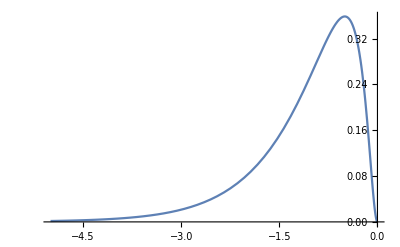

```mathematica
Plot[Log[1+Abs[Gam[k]]^2]/((k-1)^2+1),{k,-5,0}]
```

```mathematica
xi=-1;eta=1;
NIntegrate[Log[1+Abs[Gam[k]]^2]/((k-xi)^2+eta)*(k-xi),{k,-∞,-1}]*(1/Pi)
NIntegrate[Log[1+Abs[Gam[k]]^2]/((k-xi)^2+eta),{k,-∞,-1}]*(-eta/Pi)
```

-0.236191+0. ⅈ

-0.354645

```mathematica
xi=-2;eta=1;
NIntegrate[Log[1+Abs[Gam[k]]^2]/((k-xi)^2+eta)*(k-xi),{k,-∞,-2}]*(1/Pi)
NIntegrate[Log[1+Abs[Gam[k]]^2]/((k-xi)^2+eta),{k,-∞,-2}]*(-eta/Pi)
```

-0.107931+0. ⅈ

-0.180415

#### poles

```mathematica
polelist1={-1+1.I,-2+1.I};
nc1={100000,2};
polelist2={};(*zeros of a*)
nc2={};
```

```mathematica
(*polelist1={};
nc1={};
polelist2={};
nc2={};*)
```

```mathematica
(*200 length, 100 points with x=1 seems to be just not enough, x=0.9 was not bad*)
```

```mathematica
SetParams[.4,.1,10.^(-13),20,40,100];
(*SetParams[nu_,rad1_,tol_,sN_,bN_,length_]*)
(*SetScatteringData[aa,bb,ρ,Poles]*)
SetScatteringData[gam,Gam,polelist1,nc1,polelist2,nc2];
h[k_]:=Abs[mm/(k-2*(1-I))^4];
Setrsamp[h];
Settimeflag[True];
```

#### sol

```mathematica
qNLS//Clear;
qNLS[x_,t_]:=qNLS[x,t]=NLSAuto[x,t];
```

```mathematica
xx=0.4;tt=0.1;
qNLS[xx,tt]
```

Region: 1 (0.4,0.1) 1) Construct: 1.70313  1) Solve: 3.59375  2) Construct: 10.  2) Solve: 1.375

-1.67173+0.162513 ⅈ

```mathematica
qNLS[3.,0.5]
```

Region: 1 (3.,0.5) 1) Construct: 1.64063  1) Solve: 0.34375  2) Construct: 3.875  2) Solve: 1.51563

-1.11265+1.48464 ⅈ

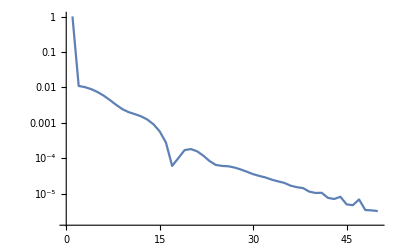
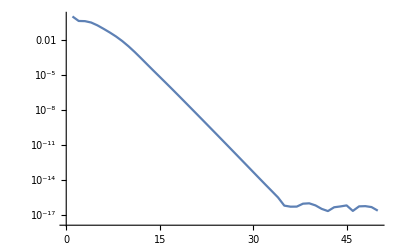
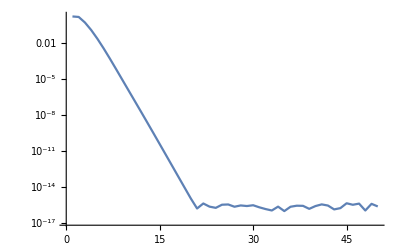
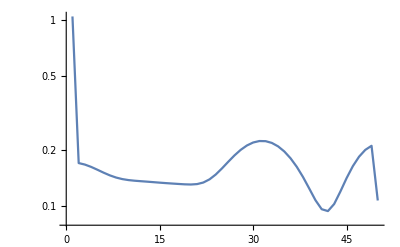
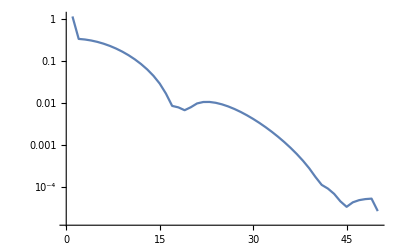
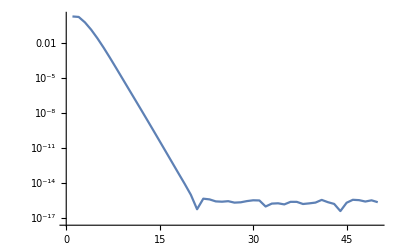
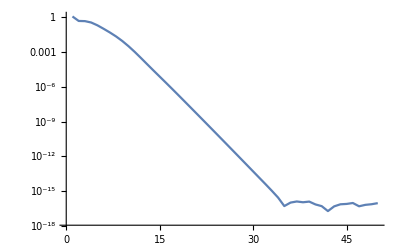
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@rhp1
```

```mathematica
mylNLSdata=NotebookDirectory[]<>"mylNLSdatafile";(*file name*)
```

```mathematica
Get["mylNLSdatafile"];
```

```mathematica
(*Save[mylNLSdata,qNLS]*)
```

```mathematica
ks={-1+1.I,-2+1.I};
cs={100000,2};
```

```mathematica
Clear[theta,M,F]
z1=ks[[1]];z2=ks[[2]];c1=2/cs[[1]]*Exp[-I*(Pi/2-0.3)];c2=2/cs[[2]]*Exp[I*(Pi/2+0.5)];
theta[x_,t_,z_]:=-I*z*x-2*I*z^2*t;
M[x_,t_]:=({{(Exp[-theta[x,t,z1]-cc[theta[x,t,z1]]]+cc[c1]*c1*Exp[theta[x,t,z1]+cc[theta[x,t,z1]]])/(cc[z1]-z1), (Exp[-theta[x,t,z2]-cc[theta[x,t,z1]]]+cc[c1]*c2*Exp[theta[x,t,z2]+cc[theta[x,t,z1]]])/(cc[z1]-z2)}, {(Exp[-theta[x,t,z1]-cc[theta[x,t,z2]]]+cc[c2]*c1*Exp[theta[x,t,z1]+cc[theta[x,t,z2]]])/(cc[z2]-z1), (Exp[-theta[x,t,z2]-cc[theta[x,t,z2]]]+cc[c2]*c2*Exp[theta[x,t,z2]+cc[theta[x,t,z2]]])/(cc[z2]-z2)}});
F[x_,t_]:=({{0, Exp[-cc[theta[x,t,z1]]], Exp[-cc[theta[x,t,z2]]]}, {c1*Exp[theta[x,t,z1]], M[x,t][[1,1]], M[x,t][[2,1]]}, {c2*Exp[theta[x,t,z2]], M[x,t][[1,2]], M[x,t][[2,2]]}});
f2[x_,t_]:=Refine[-2I*Det[F[x,t]]/Det[M[x,t]],{Element[x,Reals],Element[t,Reals]}];
```

```mathematica
Manipulate[Plot[Abs[f2[x+0.4,tt]],{x,0.,30},PlotRange->All],{tt,0,3.,0.1}]
```

```mathematica
QQ=({{11, 12}, {21, 22}});
QQ[[1,2]]
```

12

```mathematica
tvec[[jj]]
```

0.1

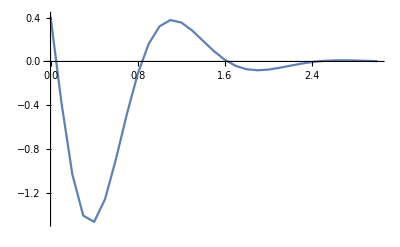

```mathematica
TablePlot[Re[f2[x+0.4,0.1]],{x,0.,3.,0.1},PlotRange->All]
```

```mathematica
f2[.4,0.1]//Abs
```

1.99996

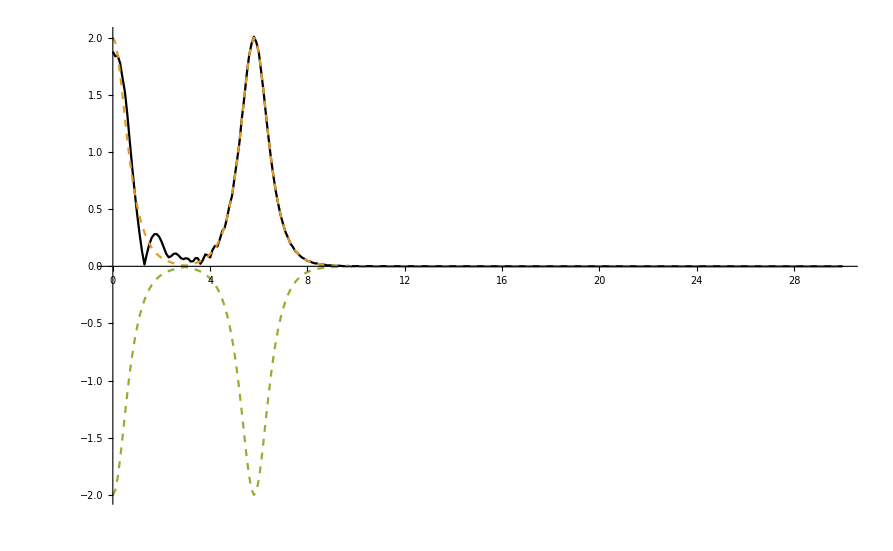

```mathematica
TablePlot[{Abs[qNLS[x,0.1]],Abs[f2[x+0.4,0.1]],-Abs[f2[x+0.4,0.1]]},{x,0.,30.,0.1},PlotRange->All,PlotStyle->{Black,Dashed,Dashed}]
```

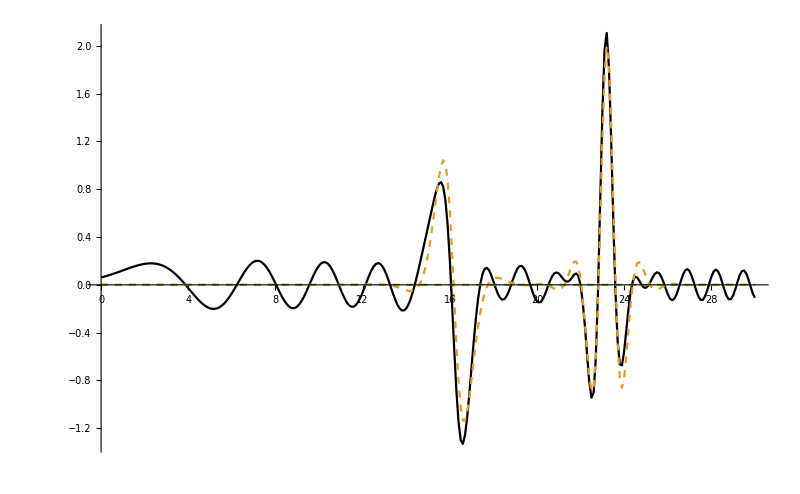

```mathematica
TablePlot[{Re[qNLS[x,2.9]],Re[f2[x+0.4,2.9]],-Abs[f2[x+0.4,2.9]]*0},{x,0.,30.,0.1},PlotRange->All,PlotStyle->{Black,Dashed,Dashed}]
```

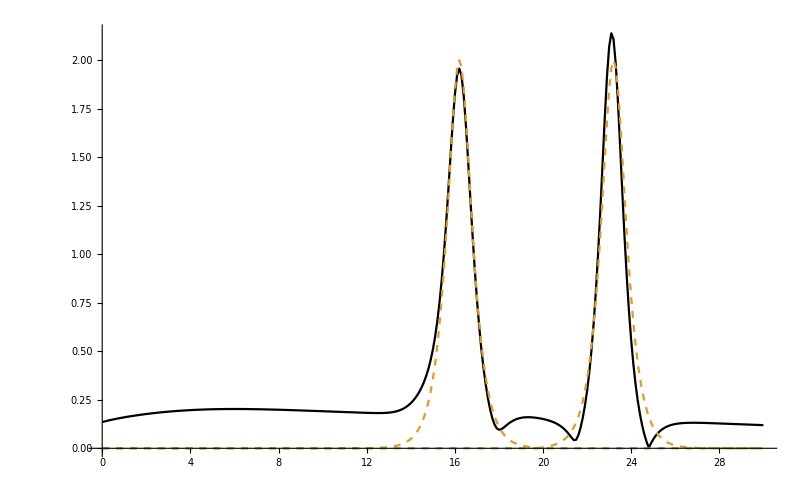

```mathematica
TablePlot[{Abs[qNLS[x,2.9]],Abs[f2[x+0.4,2.9]],-Abs[f2[x+0.4,2.9]]*0},{x,0.,30.,0.1},PlotRange->All,PlotStyle->{Black,Dashed,Dashed}]
```

```mathematica
tt=5;
xxmin1=4*tt+2
xxmax1=4*tt+7
xxmin2=8*tt-2
xxmax2=8*tt+2
```

22

27

38

42

```mathematica
xi=1;eta=1;
NIntegrate[Log[1+Abs[Gam[k]]^2]/((k-xi)^2+eta)*(k-xi),{k,-∞,-1}]*(1/Pi)
NIntegrate[Log[1+Abs[Gam[k]]^2]/((k-xi)^2+eta),{k,-∞,-1}]*(-eta/Pi)/2
```

-0.194413+0. ⅈ

-0.0348861

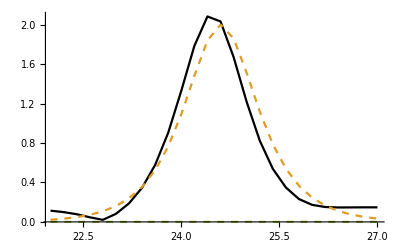

```mathematica
TablePlot[{Abs[qNLS[x,tt]],Abs[f2[x+0.4,tt]],-Abs[f2[x+0.4,2.9]]*0},{x,xxmin1,xxmax1,0.2},PlotRange->All,PlotStyle->{Black,Dashed,Dashed}]
```

```mathematica
xi=2;eta=1;
NIntegrate[Log[1+Abs[Gam[k]]^2]/((k-xi)^2+eta)*(k-xi),{k,-∞,-2}]*(1/Pi)
NIntegrate[Log[1+Abs[Gam[k]]^2]/((k-xi)^2+eta),{k,-∞,-2}]*(-eta/Pi)/2
```

-0.0597884+0. ⅈ

-0.00620492

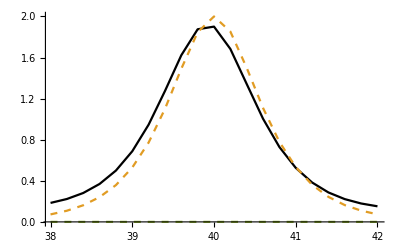

```mathematica
TablePlot[{Abs[qNLS[x,tt]],Abs[f2[x+0.4,tt]],-Abs[f2[x+0.4,2.9]]*0},{x,xxmin2,xxmax2,0.2},PlotRange->All,PlotStyle->{Black,Dashed,Dashed}]
```

```mathematica
domainOutput
```

-Graphics-

```mathematica
Clear[Solution]
Solution[x_,t_]:=Solution[x,t]=qNLS[x,t];
xmax=30.;tmax=3.0;
dx=0.1;
dt=0.2;(*was 0.1*)
Clear[data]
data[tt_]:=Flatten[Table[{x,t,Abs[Solution[x,t]]},{t,tt,tt,0.5},{x,0.,xmax,dx}],1];(*tt 0.5 does not matter this generates a line in x direction*)
```

```mathematica
tvec[[8]]
```

1.5

```mathematica
tvec[[8]]-1.5
```

2.22045×10^-16

```mathematica
Solution[0.6,tvec[[8]]]
```

0.272609-0.120937 ⅈ

```mathematica
Abs[qNLS[6,0.1] ]
```

1.87129

```mathematica
qNLS[0.6,1.5]
```

0.272609-0.120937 ⅈ

```mathematica
Abs[f2[6,0.1]]
```

1.83234

```mathematica
tvec=Table[t,{t,0.1,tmax,dt}];
```

```mathematica
data2[tt_]:=Flatten[Table[{x,t,Re[f2[x,t]]},{t,tt,tt,0.5},{x,0.,xmax,dx/20}],1];
```

```mathematica
nlssol=Show[Table[ListPointPlot3D[data[tt],AxesLabel->{"x","t","q"},PlotStyle->{Black,Thick,GrayLevel[tt*0.2]},LabelStyle->Directive[Black],PlotRange->All]/.Point->Line,{tt,Join[Table[j,{j,0.1,tmax,dt}],{}]}],PlotRange->{{-0.1,xmax},{0,tmax},All},ImageSize->500,BaseStyle->{FontSize->20}]
```

-Graphics3D-

```mathematica
p1=-Graphics3D-;
```

```mathematica
nlssol1=Show[Table[ListPointPlot3D[data[tt],AxesLabel->{"x","t","q"},PlotStyle->{Black,Thick},LabelStyle->Directive[Black],PlotRange->All,Filling->Bottom,FillingStyle->Directive[White,Opacity[10.],Lighting->{"Ambient",White}]]/.Point->Line,{tt,Join[Table[j,{j,0.1,2.5,dt}],{}]}],PlotRange->{{-0.1,xmax},{0,tmax},All},ImageSize->500,BaseStyle->{FontSize->20}]
```

-Graphics3D-

```mathematica
nlssol=Show[Table[ListPointPlot3D[data2[tt],AxesLabel->{"x","t","q"},PlotStyle->{Black,Thick},LabelStyle->Directive[Black],PlotRange->All,Filling->Bottom,FillingStyle->Directive[White,Opacity[10.],Lighting->{"Ambient",White}]]/.Point->Line,{tt,Join[Table[j,{j,0.1,tmax,dt}],{}]}],PlotRange->{{-0.1,xmax},{0,tmax},All},ImageSize->500,BaseStyle->{FontSize->20}]
```

$Aborted

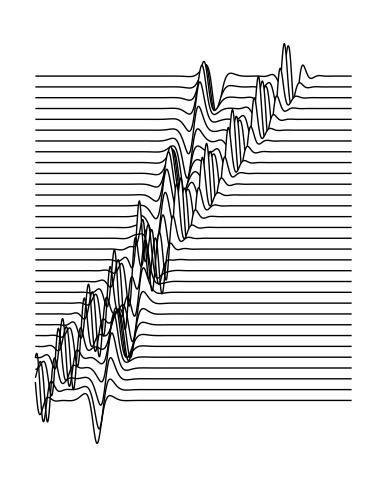

```mathematica
Show[Table[Plot[Re[f2[x,t]]+t*5,{x,0,30},PlotStyle->Directive[Black,Thick],Filling->Bottom,FillingStyle->Directive[White,Opacity[1.]],Axes->False,AspectRatio->Automatic,ImageSize->{500,630},PlotRange->All],{t,3,0,-0.1}]]
```

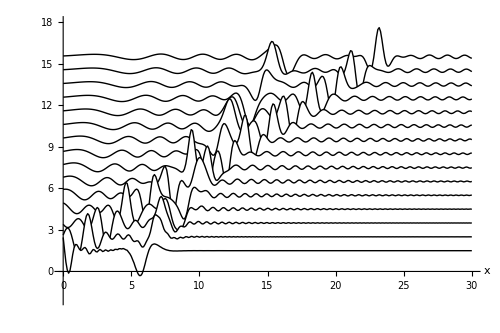

```mathematica
nlssol2=Show[Table[TablePlot[Re[Solution[x,t]]+t*5+1,{x,0.,30.,dx},PlotStyle->Directive[Black,Thick],LabelStyle->Directive[Black],Filling->Bottom,FillingStyle->Directive[White,Opacity[1.]],AxesLabel->{"x"},Axes->{True,False},AspectRatio->Automatic,ImageSize->500,PlotRange->{-2,18}],{t,Reverse[tvec]}],BaseStyle->{FontSize->20}]
```

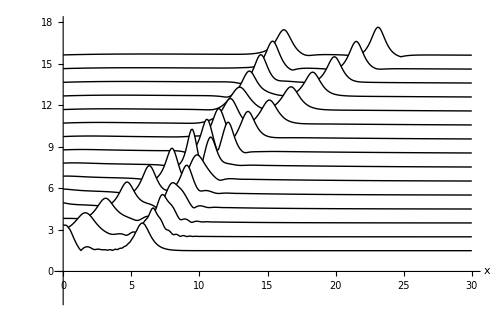

```mathematica
nlssol3=Show[Table[TablePlot[Abs[Solution[x,t]]+t*5+1,{x,0.,30.,dx},PlotStyle->Directive[Black,Thick],LabelStyle->Directive[Black],Filling->Bottom,FillingStyle->Directive[White,Opacity[1.]],AxesLabel->{"x"},Axes->{True,False},AspectRatio->Automatic,ImageSize->500,PlotRange->{-2,18}],{t,Reverse[tvec]}],BaseStyle->{FontSize->20}]
```

```mathematica
Export["2solitondressing2.pdf",nlssol2]
Export["2solitondressing3.pdf",nlssol3]
```

2solitondressing2.pdf

2solitondressing3.pdf

```mathematica
Export["2solitondressing.pdf",p1]
```

2solitondressing.pdf

```mathematica
nlssol=Show[Table[ListPointPlot3D[data[tt],AxesLabel->{"x","t","q"},PlotStyle->{Black,Thick,GrayLevel[tt*0]},LabelStyle->Directive[Black,Bold],PlotRange->All]/.Point->Line,{tt,Join[Table[j,{j,0.1,tmax,dt}],{}]}],PlotRange->{{-0.1,xmax},{0,tmax},{-0.1,0.1}},ImageSize->500,BaseStyle->{FontSize->20}]
```

-Graphics3D-

```mathematica
tvec
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9}

```mathematica
tvec=Table[t,{t,0.1,tmax,dt*2}];
```

```mathematica
qNLS[0.,0.9]
```

0.42366-0.15846 ⅈ

```mathematica
tvec[[15]]
```

2.9

```mathematica
xmax
```

```mathematica
xvec1=Sort[Join[Table[x,{x,0.,xmax,0.2}],Table[x,{x,0.,7.,0.1/2}]]];
p1=TablePlot[{Re[qNLS[x,tvec[[1]]]],Abs[f2[x+0.4,tvec[[1]]]],-Abs[f2[x+0.4,tvec[[1]]]]},{x,xvec1},PlotRange->All,PlotStyle->{{Black},{Dashed,Black},{Dashed,Black}},GridLines->Automatic,ImageSize->500,BaseStyle->{FontSize->20},LabelStyle->Directive[Black],AxesLabel->{"x"}]
```

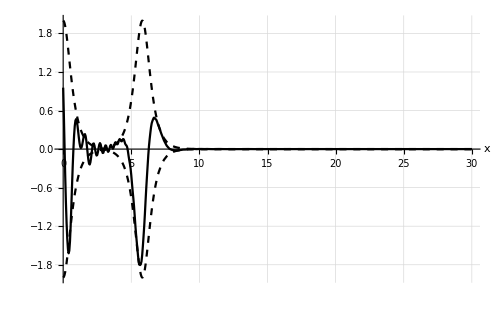

```mathematica
xvec2=Sort[Join[Table[x,{x,0.,xmax,0.2}],Table[x,{x,15.,30.,0.1}]]];
p2=TablePlot[{Re[qNLS[x,tvec[[15]]]],Abs[f2[x+0.4,tvec[[15]]]],-Abs[f2[x+0.4,tvec[[15]]]]},{x,xvec2},PlotRange->All,PlotStyle->{{Black},{Dashed,Black},{Dashed,Black}},GridLines->Automatic,ImageSize->500,BaseStyle->{FontSize->20},LabelStyle->Directive[Black],AxesLabel->{"x"}]
```

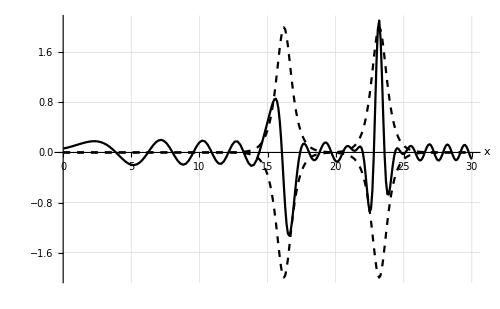

```mathematica
(*start of comparison with asymptotic formula*)
```

```mathematica
envo[x_,t_]:=1/Sqrt[t]*Sqrt[(1/4/Pi)*Log[1+Abs[Gam[-x/4/t]]^2]];
al[x_,t_]:=Sqrt[(1/4/Pi)*Log[1+Abs[Gam[-x/4/t]]^2]];
```

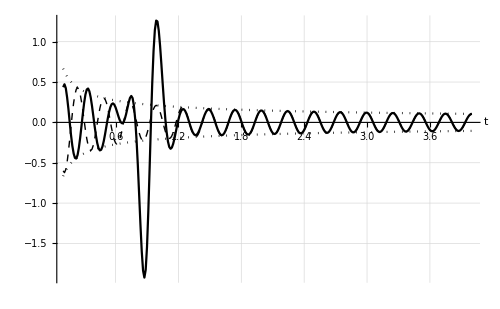

```mathematica
kk=10;
tvec2=Table[t,{t,0.1,4.,0.1/8}];
pshift10=0.4;
asymp10[x_,t_]:=1/Sqrt[t]*Sqrt[(1/4/Pi)*Log[1+Abs[Gam[-x/4/t]]^2]]*Exp[I*x^2/t/4+2I*al[x,t]^2*Log[t]+I*pshift10];
p3=TablePlot[{Re[qNLS[kk*t,t]],envo[kk*t,t],-envo[kk*t,t],Re[asymp10[kk*t,t]]},{t,Join[tvec2,{}]},PlotRange->All,PlotStyle->{{Black},{Dotted,Black},{Dotted,Black},{Black,Dashed,Thick}},GridLines->Automatic,ImageSize->500,BaseStyle->{FontSize->20},LabelStyle->Directive[Black],AxesLabel->{"t"}]
```

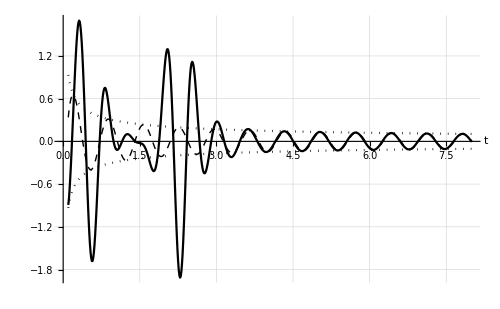

```mathematica
kk=6;
tvec3=Sort[Join[Table[t,{t,0.1,8.,0.1/4}],Table[t,{t,0.1,4.,0.1/8}]]];
pshift6=-1.7;
asymp6[x_,t_]:=1/Sqrt[t]*Sqrt[(1/4/Pi)*Log[1+Abs[Gam[-x/4/t]]^2]]*Exp[I*x^2/t/4+2I*al[x,t]^2*Log[t]+I*pshift6];
p4=TablePlot[{Re[qNLS[kk*t,t]],envo[kk*t,t],-envo[kk*t,t],Re[asymp6[kk*t,t]]},{t,Join[tvec3,{}]},PlotRange->All,PlotStyle->{{Black},{Dotted,Black},{Dotted,Black},{Black,Dashed,Thick}},GridLines->Automatic,ImageSize->500,BaseStyle->{FontSize->20},LabelStyle->Directive[Black],AxesLabel->{"t"}]
```

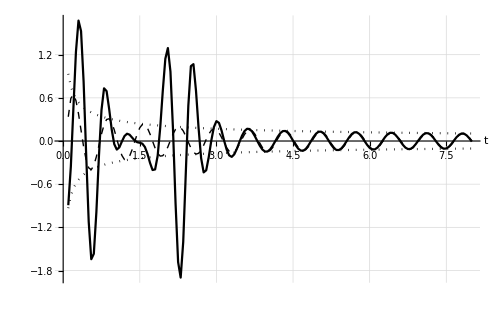

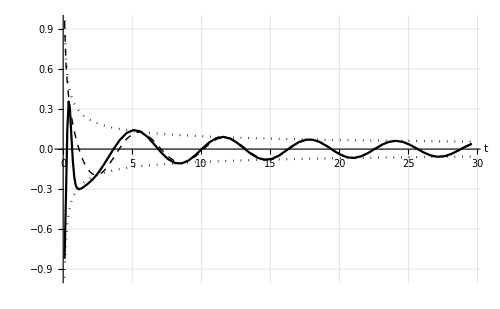

```mathematica
kk=2;
tvec4=Sort[Join[Table[t,{t,0.1,30.,0.5}],Table[t,{t,0.1,3.,0.1}]]];
pshift2=0.4;
asymp2[x_,t_]:=1/Sqrt[t]*Sqrt[(1/4/Pi)*Log[1+Abs[Gam[-x/4/t]]^2]]*Exp[I*x^2/t/4+2I*al[x,t]^2*Log[t]+I*pshift2];p5=TablePlot[{Re[qNLS[kk*t,t]],envo[kk*t,t],-envo[kk*t,t],Re[asymp2[kk*t,t]]},{t,tvec4},PlotRange->All,PlotStyle->{{Black},{Dotted,Black},{Dotted,Black},{Black,Dashed,Thick}},GridLines->Automatic,ImageSize->500,BaseStyle->{FontSize->20},LabelStyle->Directive[Black],AxesLabel->{"t"}]
```

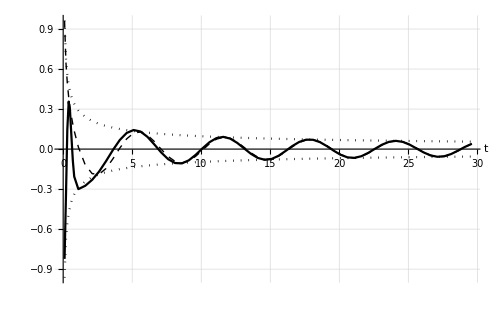

```mathematica
qNLS[1.,0.1]
```

0.436314-0.130227 ⅈ

```mathematica
tvec
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9}

```mathematica
Join[{0.1,0.2},{0.1}]
```

{0.1,0.2,0.1}

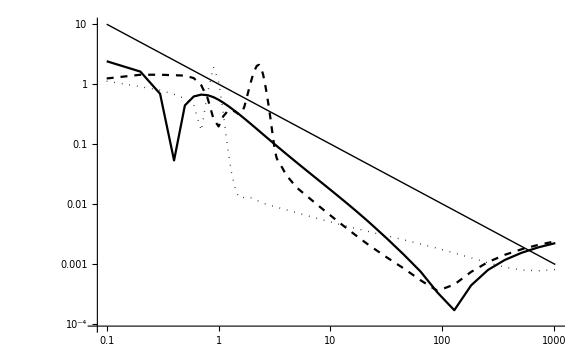

```mathematica
pshift2=0.36;
pshift6=-1.69;
pshift10=0.5;
tvec5=Sort[Join[Table[t,{t,0.1,4.,0.1}],Table[t,{t,4.0,20.,1.}],Table[2^t,{t,4.,10.,0.5}]]];
p345=TablePlot[{Abs[qNLS[2*t,t]-asymp2[2*t,t]],Abs[qNLS[6*t,t]-asymp6[6*t,t]],Abs[qNLS[10*t,t]-asymp10[10*t,t]],1/t},{t,tvec5},PlotStyle->{{Black},{Black,Dashed},{Black,Dotted,Thick},{Black,Thick}},ScalingFunctions->{"Log","Log"}]
```

```mathematica
Export["dressing1.pdf",p1]
Export["dressing2.pdf",p2]
```

```mathematica
Export["dressing3.pdf",p3]
Export["dressing4.pdf",p4]
Export["dressing5.pdf",p5]
```

dressing3.pdf

dressing4.pdf

dressing5.pdf

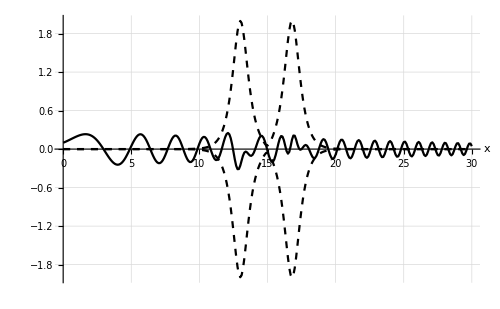

```mathematica
xvec3=Sort[Join[Table[x,{x,0.,xmax,0.1}]]];
p6=TablePlot[{Re[qNLS[x,tvec[[11]]]-f2[x+0.4,tvec[[11]]]],Abs[f2[x+0.4,tvec[[11]]]],-Abs[f2[x+0.4,tvec[[11]]]]},{x,xvec3},PlotRange->All,PlotStyle->{{Black},{Dashed,Black},{Dashed,Black}},GridLines->Automatic,ImageSize->500,BaseStyle->{FontSize->20},LabelStyle->Directive[Black],AxesLabel->{"x"}]
```

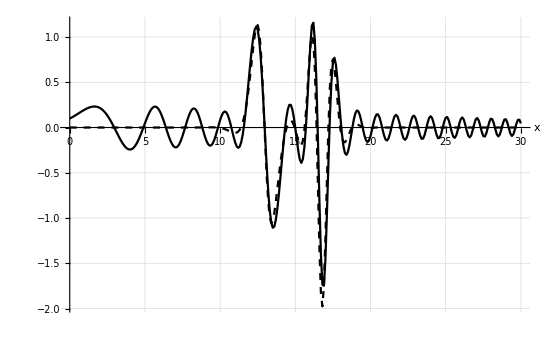

```mathematica
p6=TablePlot[{Re[qNLS[x,tvec[[11]]]],Re[f2[x+0.48,tvec[[11]]]]},{x,xvec3},PlotRange->All,PlotStyle->{{Black},{Dashed,Black},{Dashed,Black}},GridLines->Automatic,ImageSize->500,BaseStyle->{FontSize->20},LabelStyle->Directive[Black],AxesLabel->{"x"}]
```

```mathematica
(*try capture the phase*)
```

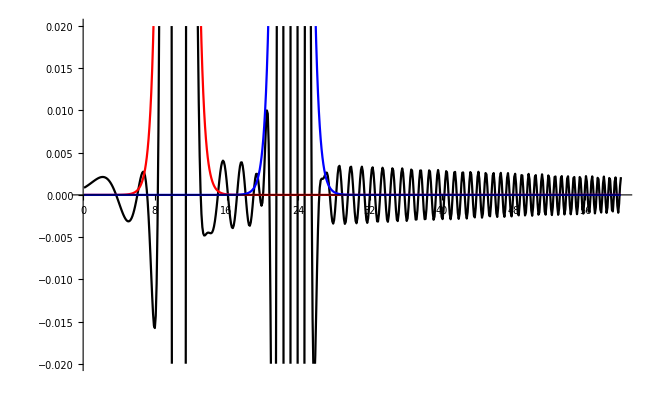

```mathematica
ttt=3.;
p2=TablePlot[{Re[qNLS[x,ttt]],Abs[ss1[x,ttt]],Abs[ss2[x,ttt]]},{x,0.1,xmax*3,dx},PlotRange->{-0.02,0.02},PlotStyle->{Black,Red,Blue}]
```

```mathematica
Export["2solitont3.pdf",p2]
```

2solitont3.pdf

```mathematica
TablePlot[Re[qNLS[x,3.]],{x,0.1,xmax*2,dx},PlotRange->{-0.05,0.05}]
```

Region: 1 (0.2,3.) 1) Construct: 4.09375  1) Solve: 11.9219  2) Construct: 6.20313  2) Solve: 0.484375

$Aborted

```mathematica
(*test 2 soliton solution, possibly wrong formula*)
(*def constants p1 p2, c1 c2*)
```

```mathematica
Clear[xi1,xi2,eta1,eta2,p1,p2]
```

```mathematica
p1=Sqrt[2]+2I*Sqrt[2];p2=Sqrt[2]+I*Sqrt[2];c1=0;c2=0;alpha=Log[Abs[p1-p2]/Abs[p1+cc[p2]]];
phi1=Arg[(p1-p2)/(p1+cc[p2])];
phi2=Arg[(p2-p1)/(cc[p1]+p2)];
A1=Abs[p1+cc[p1]]/Sqrt[2];
A2=Abs[p2+cc[p2]]/Sqrt[2];
o1=-I/2*p1^2;
o2=-I/2*p2^2;
```

```mathematica
xi1[x_,t_]:=Re[p1]*x*Sqrt[2]-Re[o1]*t*4+Re[c1];
xi2[x_,t_]:=Re[p2]*x*Sqrt[2]-Re[o2]*t*4+Re[c2];
eta1[x_,t_]:=Im[p1]*x*Sqrt[2]-Im[o1]*t*4+Im[c1];
eta2[x_,t_]:=Im[p2]*x*Sqrt[2]-Im[o2]*t*4+Im[c2];
```

```mathematica
f[x_,t_]:=(A1*Sech[xi1[x,t]]*Exp[I*eta1[x,t]]*(Cos[phi1]+I*Sin[phi1]*Tanh[xi2[x,t]])+A2*Sech[xi2[x,t]]*Exp[I*eta2[x,t]]*(Cos[phi2]+I*Sin[phi2]*Tanh[xi1[x,t]]))/(Cosh[alpha]+Sinh[alpha]*(Tanh[xi1[x,t]]*Tanh[xi2[x,t]]-Sech[xi1[x,t]]*Sech[xi2[x,t]]*Cos[eta1[x,t]-eta2[x,t]]))
```

```mathematica
Manipulate[Plot[Abs[f[x+1.2,t+1.6]],{x,-10,20},PlotRange->{-0,2.5},GridLines->Automatic],{t,-3,3.,0.1}]
```

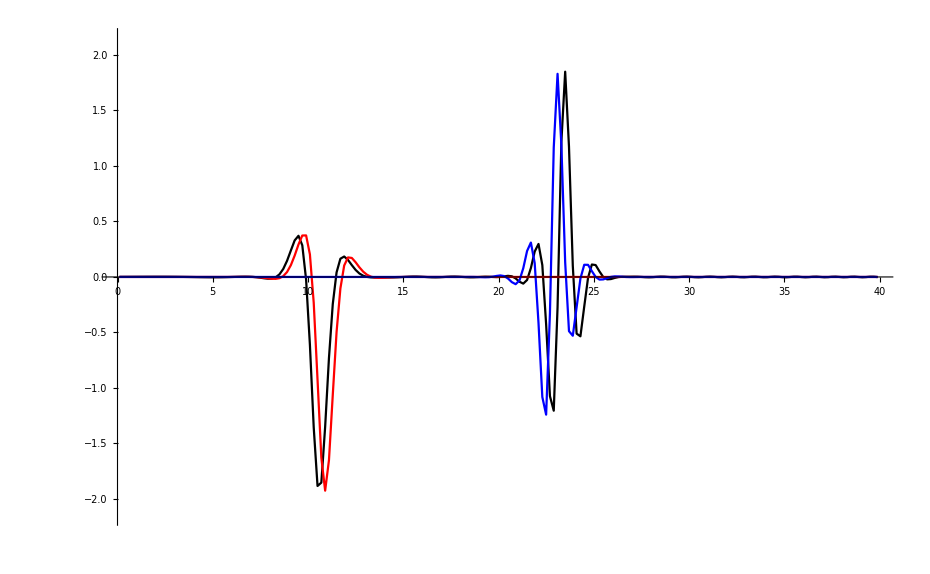

```mathematica
xi1=-1;xi2=-2;eta1=1;eta2=1;x01=-1.2;x02=-1.1;
ss1[x_,t_]:=2*eta1*Exp[-4*I*t(xi1^2-eta1^2)-2I x xi1]*Sech[2*eta1*(4*t*xi1+x-x01)];
ss2[x_,t_]:=2*eta2*Exp[-4*I*t(xi2^2-eta2^2)-2I x xi2]*Sech[2*eta2*(4*t*xi2+x-x02)];
p3=TablePlot[{Re[qNLS[x,3.]],Re[ss1[x,3]],Re[ss2[x,3]]},{x,0.1,xmax*2,dx*2},PlotRange->{-2.15,2.15},PlotStyle->{Black,Red,Blue}]
```

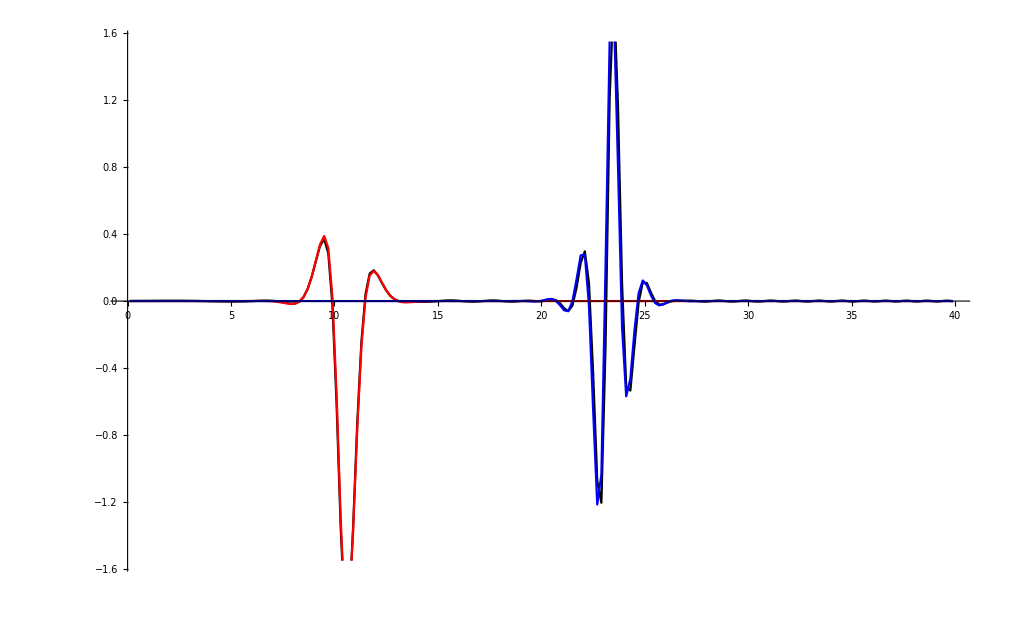

```mathematica
xi1=-1;xi2=-2;eta1=1;eta2=1;x01=-1.2;x02=-1.09;
ss1[x_,t_]:=2*eta1*Exp[-4*I*t(xi1^2-eta1^2)-2I x xi1]*Sech[2*eta1*(4*t*xi1+x-x01)];
ss2[x_,t_]:=2*eta2*Exp[-4*I*t(xi2^2-eta2^2)-2I x xi2]*Sech[2*eta2*(4*t*xi2+x-x02)];
TablePlot[{Re[qNLS[x,3.]],Re[ss1[x+0.3,3]],Re[ss2[x-0.33,3]]},{x,0.1,xmax*2,dx*2},PlotRange->{-1.55,1.55},PlotStyle->{Black,Red,Blue}]
```

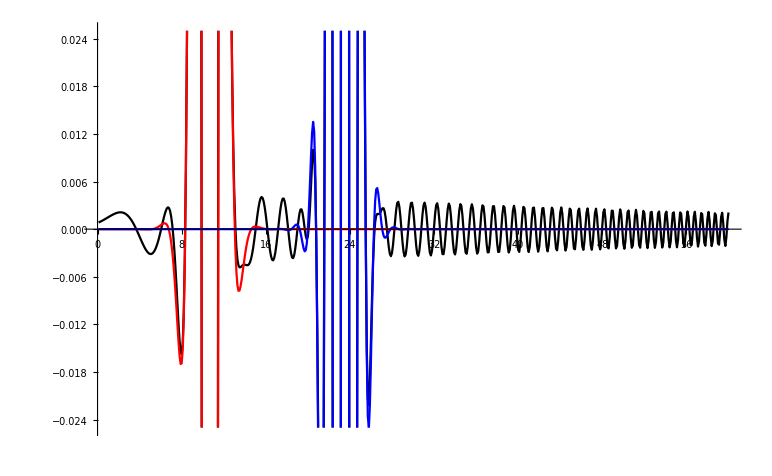

```mathematica
xi1=-1;xi2=-2;eta1=1;eta2=1;x01=-1.5;x02=-0.7;
ss1[x_,t_]:=2*eta1*Exp[-4*I*t(xi1^2-eta1^2)-2I x xi1+0.6I]*Sech[2*eta1*(4*t*xi1+x-x01)];
ss2[x_,t_]:=2*eta2*Exp[-4*I*t(xi2^2-eta2^2)-2I x xi2-1.6I]*Sech[2*eta2*(4*t*xi2+x-x02)];
TablePlot[{Re[qNLS[x,3.]],Re[ss1[x,3]],Re[ss2[x,3]]},{x,0.1,xmax*3,dx},PlotRange->{-0.025,0.025},PlotStyle->{Black,Red,Blue}]
```

0.1

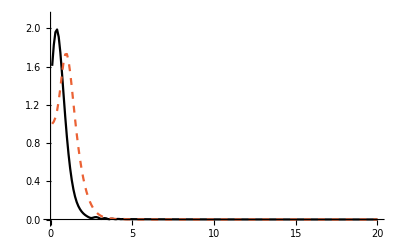

```mathematica
t1=0.1
TablePlot[{Abs[qNLS[x,t1]],Abs[ss1[x,t1]],Abs[ss2[x,t1]],Abs[f[x+1.2,t1+0.1]]},{x,0.1,xmax,dx},PlotRange->{-0.025,2.125},PlotStyle->{Black,Red,Blue,Dashed}]
```

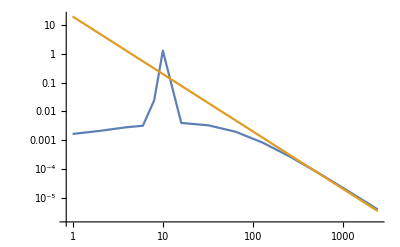

```mathematica
TablePlot[{Abs[qNLS[x,3]],20/x^2},{x,{1.,2.,4.,6.,8.,10.,16.,32.,64.,128.,256.,512.,1024.,2048.,2400.}},ScalingFunctions->{"Log","Log"}]
```

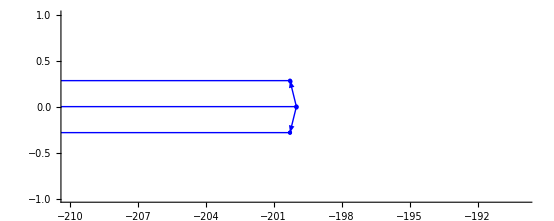

```mathematica
Show[DomainPlot[rhp1],PlotRange->{{-210,-190},{-1,1}}]
```

```mathematica
J[1][4096.,3]
```

{{Private`G1[4096.,3][#1]&,Private`G1[4096.,3][#1]&,L[4096.,3][#1]&,L[4096.,3][#1]&,DD[#1]&,U[4096.,3][#1]&,U[4096.,3][#1]&,Private`G3[4096.,3][#1]&,Private`G3[4096.,3][#1]&},{Line[{0.282843+400.283 ⅈ,0.282843+200.283 ⅈ}],Line[{0.282843+200.283 ⅈ,-200.}],Line[{-200.,-200.283-0.282843 ⅈ}],Line[{-200.283-0.282843 ⅈ,-400.283-0.282843 ⅈ}],Line[{-200.,-400.}],Line[{-200.,-200.283+0.282843 ⅈ}],Line[{-200.283+0.282843 ⅈ,-400.283+0.282843 ⅈ}],Line[{0.282843-400.283 ⅈ,0.282843-200.283 ⅈ}],Line[{0.282843-200.283 ⅈ,-200.}]},{100,100,100,100,100,100,100,100,100}}

```mathematica
Jadapt[1][4096.,3]
```

{{L[4096.,3][#1]&,L[4096.,3][#1]&,DD[#1]&,U[4096.,3][#1]&,U[4096.,3][#1]&},{Line[{-200.+0. ⅈ,-200.283-0.282843 ⅈ}],Line[{-200.283-0.282843 ⅈ,-344.12-0.282843 ⅈ}],Line[{-200.,-400.}],Line[{-200.+0. ⅈ,-200.283+0.282843 ⅈ}],Line[{-200.283+0.282843 ⅈ,-344.12+0.282843 ⅈ}]},{100,100,100,100,100}}

```mathematica
200*4*3
```

2400

```mathematica
ff[z_]:=1+(λ Conjugate[Gam[Conjugate[z]]]+gam[z])*(λ Conjugate[gam[Conjugate[z]]]+Gam[z])
```

```mathematica
ff[-200.28284271247463+0.28284271247461906 ⅈ]
```

1.+3.25694×10^-12 ⅈ

```mathematica
θ[x_,t_][z_]:=2 I (2 t z^2+x z);
Exp[θ[4096,3][-200.28284271247463-0.28284271247461906 ⅈ]]
```

1.2535162723301×10^415+6.6334420965495×10^415 ⅈ

```mathematica
mRHWellPosed[rhp1]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,0},{-2.60041994171865×10^410-1.61251194477504×10^411 ⅈ,1.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,-2.60041994171865×10^410+1.61251194477504×10^411 ⅈ},{0,1.}} may contain significant numerical errors.

((1. | 0
0 | 1.) | -400.
(1. | 0
0 | 1.) | -344.12-0.282843 ⅈ
(1. | 0
0 | 1.) | -344.12+0.282843 ⅈ
(1. | 0
-5.9×10^397-3.7×10^398 ⅈ | 1.) | -200.283-0.282843 ⅈ
(1. | -5.9×10^397+3.7×10^398 ⅈ
0 | 1.) | -200.283+0.282843 ⅈ
(1. | -0.0000211603-0.0000118679 ⅈ
-0.0000211603+0.0000118679 ⅈ | 1.) | -200.)

```mathematica
Abs[qNLS[30.,3]]
Abs[qNLS[40.,3]]
Abs[qNLS[50.,3]]
Abs[qNLS[60.,3]]
Abs[qNLS[120.,3]]
```

0.0034036

0.00292943

0.00248544

0.00210718

0.00090422

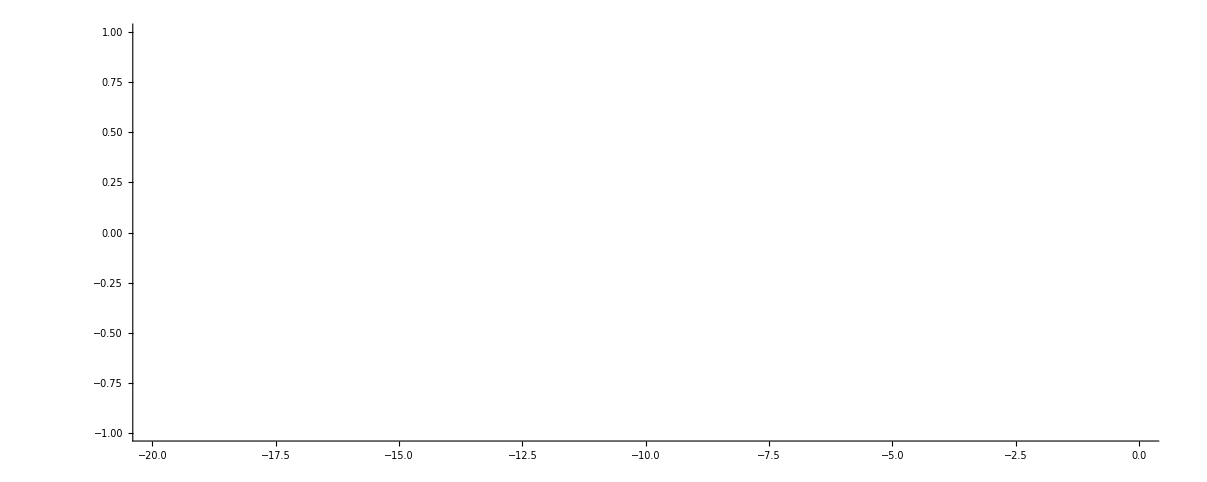

```mathematica
Show[domainOutput,PlotRange->{{-20,0},{-1,1}}]
```

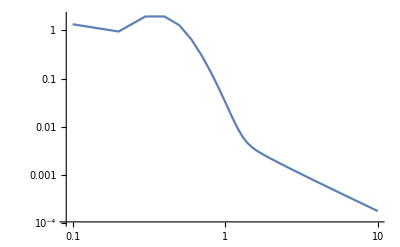

```mathematica
TablePlot[Abs[qNLS[0,t]],{t,0.,10.,0.1},ScalingFunctions->{"Log","Log"}]
```

```mathematica
qNLS[0,4.]
```

Region: 1 (0,4.) 1) Construct: 4.34375  1) Solve: 10.7969  2) Construct: 0.  2) Solve: 0.

0.000460026-0.000564117 ⅈ

Region: 1 (1.6,0.1) 1) Construct: 3.29688  1) Solve: 11.0781  2) Construct: 0.  2) Solve: 0.

Region: 1 (1.7,0.1) 1) Construct: 3.34375  1) Solve: 11.2031  2) Construct: 0.  2) Solve: 0.

Region: 1 (1.8,0.1) 1) Construct: 3.46875  1) Solve: 11.4844  2) Construct: 0.  2) Solve: 0.

Region: 1 (1.9,0.1) 1) Construct: 3.5  1) Solve: 11.3281  2) Construct: 0.  2) Solve: 0.

Region: 1 (2.,0.1) 1) Construct: 3.625  1) Solve: 10.9531  2) Construct: 0.  2) Solve: 0.

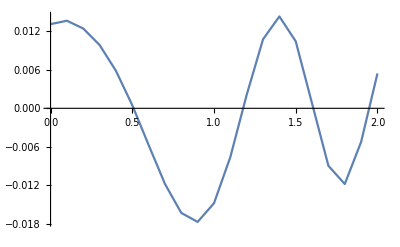

```mathematica
TablePlot[Re[qNLS[x,0.1]],{x,0.,2.,0.1}]
```

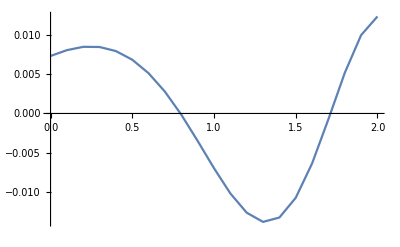

```mathematica
TablePlot[Re[qNLS[x,0.2]],{x,0.,2.,0.1}]
```

```mathematica
qNLS[0,0]
```

Region: 1 (0,0) 1) Construct: 1.57813  1) Solve: 10.1563  2) Construct: 6.1875  2) Solve: 0.515625

0.0029979-1.59703 ⅈ

```mathematica
NLS[0][1.1,0][[1]]
```

Region: 0 (1.1,0) 1) Construct: 2.54688  1) Solve: 2.34375  2) Construct: 0.  2) Solve: 0.

0.00213934+0.000825208 ⅈ

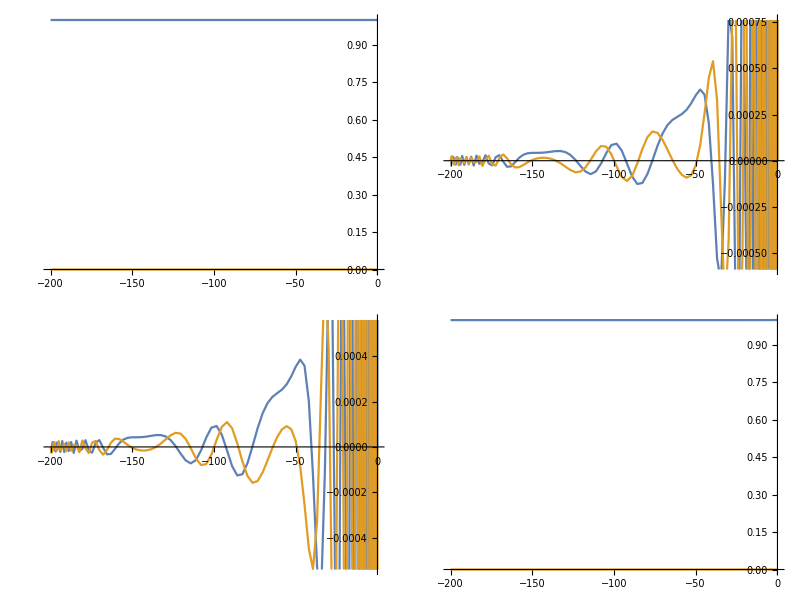
(-Graphics-)

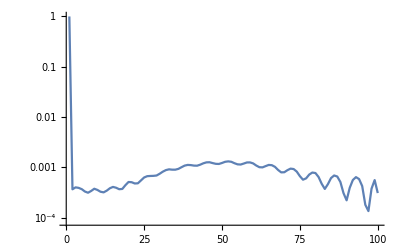

```mathematica
rhp1[[2]]
DCTPlot[rhp1[[2]]]
```

```mathematica
NLS[0][1.,0][[1]]
```

Region: 0 (1.,0) 1) Construct: 2.67188  1) Solve: 2.4375  2) Construct: 0.  2) Solve: 0.

0.00124405-0.0015909 ⅈ

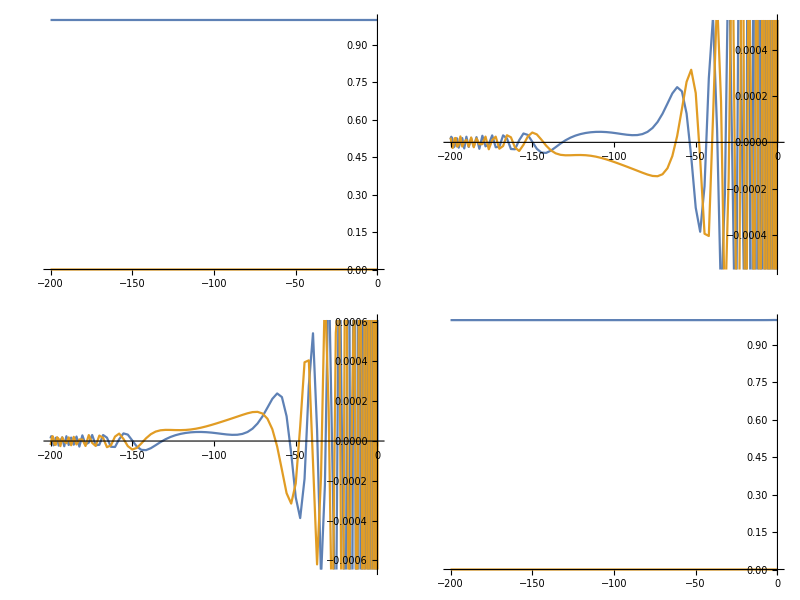
(-Graphics-)

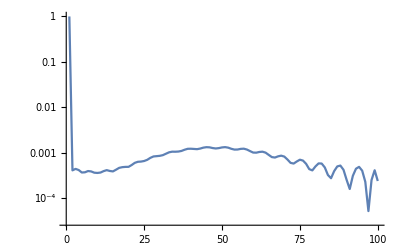

```mathematica
rhp1[[2]]
DCTPlot[rhp1[[2]]]
```

```mathematica
NLS[0][0.9,0][[1]]
```

Region: 0 (0.9,0) 1) Construct: 2.54688  1) Solve: 2.5  2) Construct: 0.  2) Solve: 0.

-3.44134×10^-6-4.70226×10^-6 ⅈ

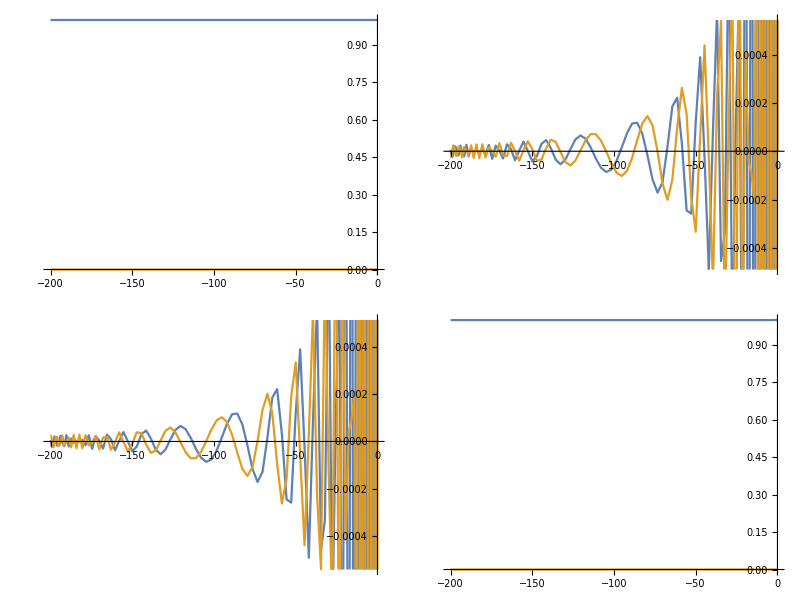
(-Graphics-)

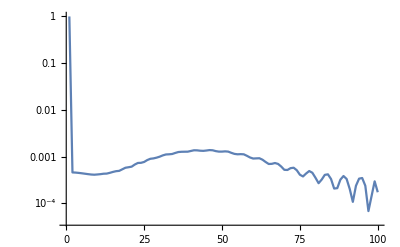

```mathematica
rhp1[[2]]
DCTPlot[rhp1[[2]]]
```

```mathematica
NLS[1][1.,0][[1]]
```

Region: 1 (1.,0) 1) Construct: 6.03125  1) Solve: 28.5  2) Construct: 0.  2) Solve: 0.

-0.000321791-0.000206158 ⅈ

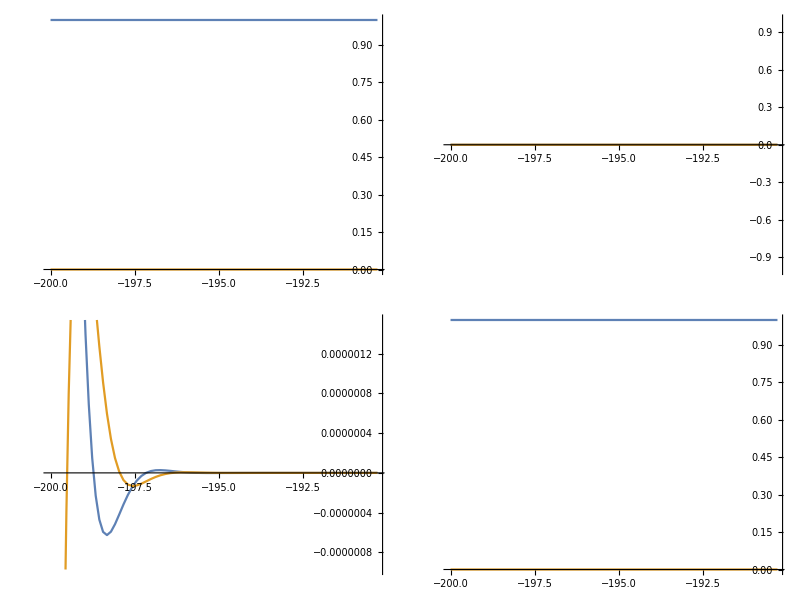
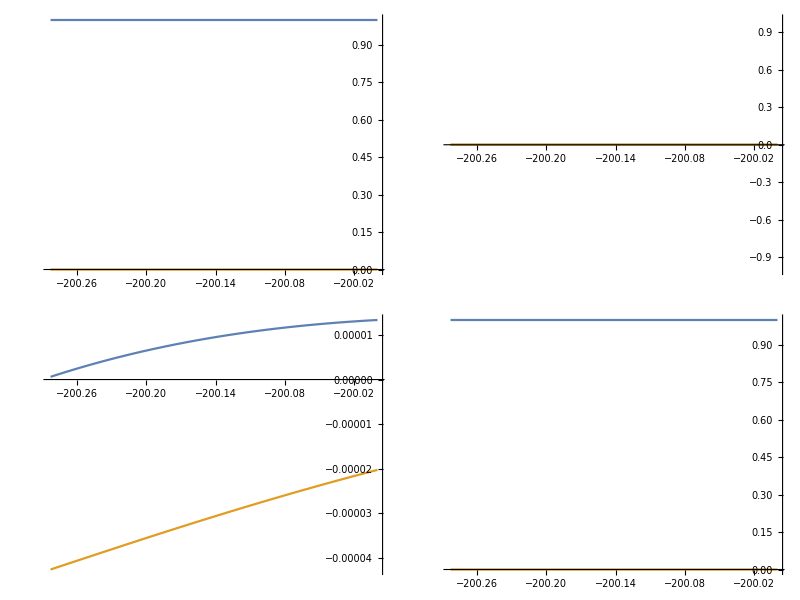
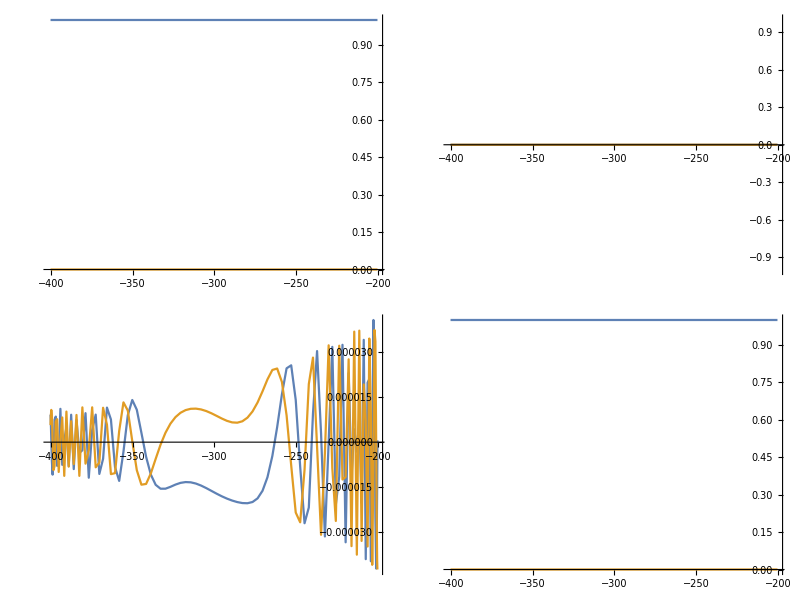
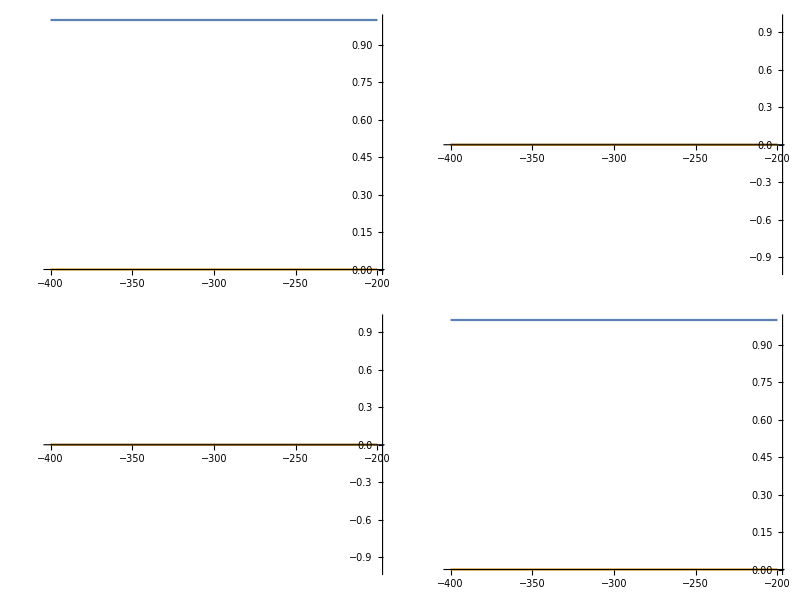
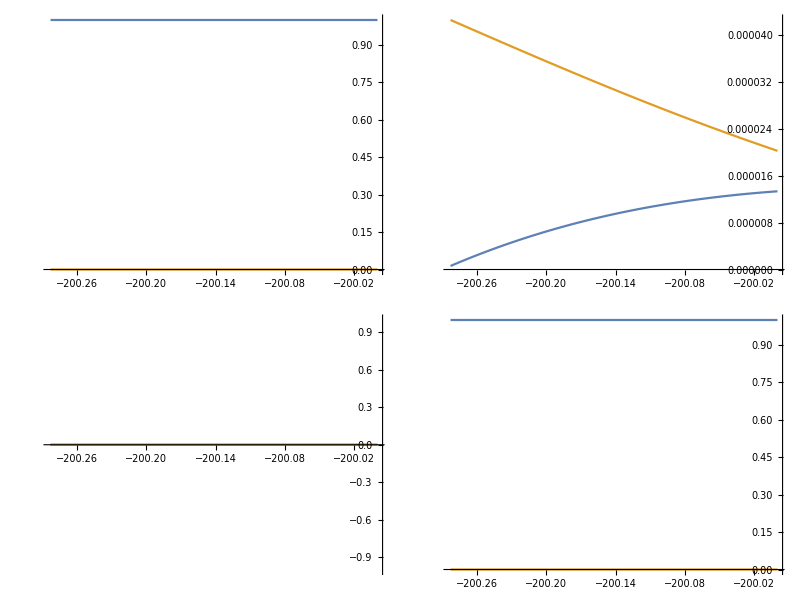
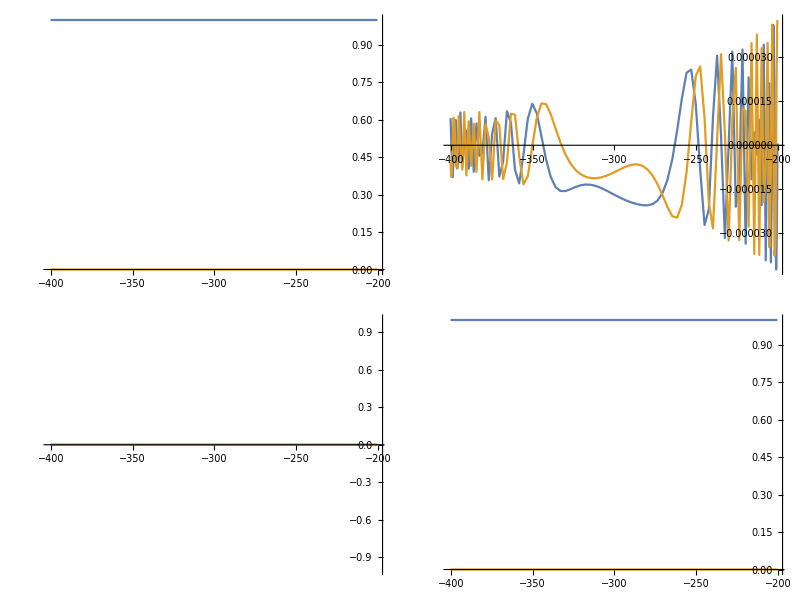
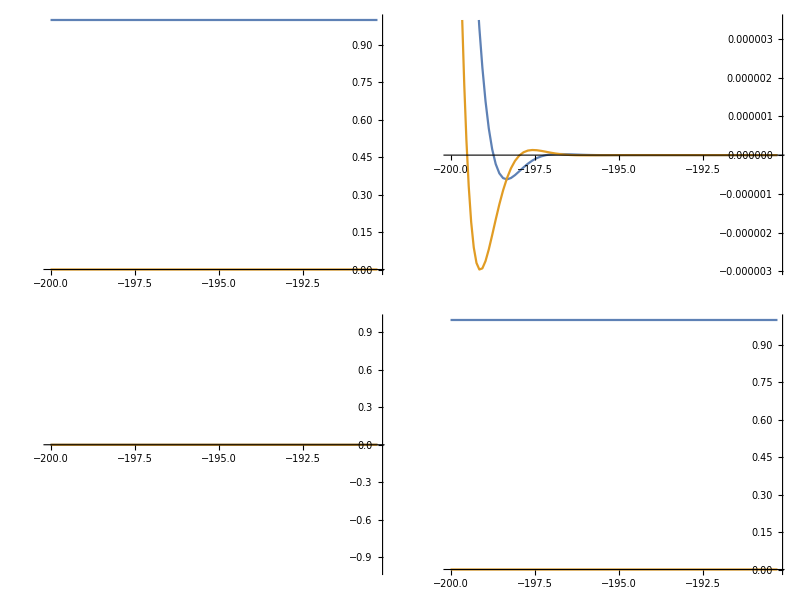
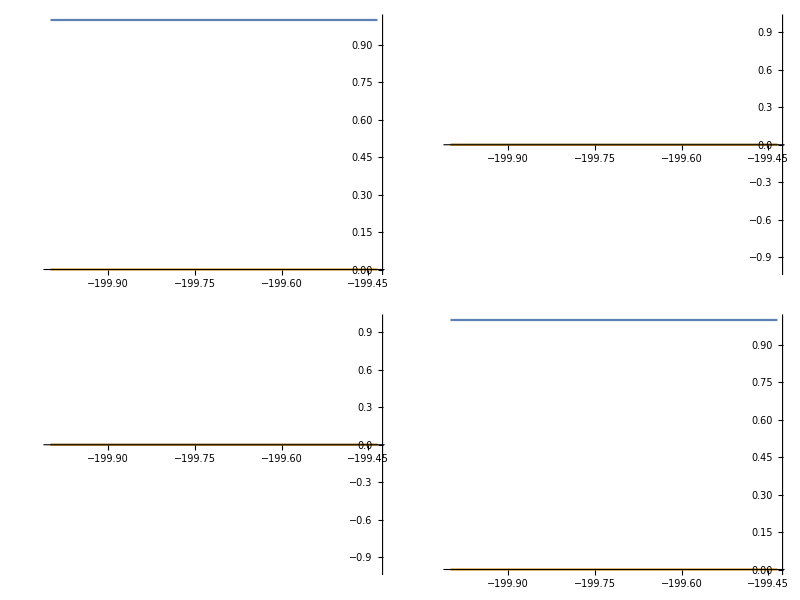
{(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
rhp1
```

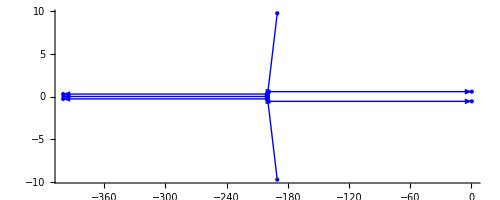

```mathematica
rhp1//DomainPlot
```

Region: 0 (0.,0) 1) Construct: 2.57813  1) Solve: 2.45313  2) Construct: 0.  2) Solve: 0.

Region: 0 (0.1,0) 1) Construct: 2.64063  1) Solve: 2.64063  2) Construct: 0.  2) Solve: 0.

Region: 0 (0.2,0) 1) Construct: 2.67188  1) Solve: 2.625  2) Construct: 0.  2) Solve: 0.

Region: 0 (0.3,0) 1) Construct: 2.65625  1) Solve: 2.46875  2) Construct: 0.  2) Solve: 0.

Region: 0 (0.4,0) 1) Construct: 2.65625  1) Solve: 2.60938  2) Construct: 0.  2) Solve: 0.

Region: 0 (0.5,0) 1) Construct: 2.67188  1) Solve: 2.76563  2) Construct: 0.  2) Solve: 0.

Region: 0 (0.6,0) 1) Construct: 2.76563  1) Solve: 2.67188  2) Construct: 0.  2) Solve: 0.

Region: 0 (0.7,0) 1) Construct: 2.6875  1) Solve: 2.79688  2) Construct: 0.  2) Solve: 0.

Region: 0 (0.8,0) 1) Construct: 2.82813  1) Solve: 2.8125  2) Construct: 0.  2) Solve: 0.

Region: 0 (0.9,0) 1) Construct: 2.92188  1) Solve: 2.8125  2) Construct: 0.  2) Solve: 0.

Region: 0 (1.,0) 1) Construct: 2.875  1) Solve: 2.65625  2) Construct: 0.  2) Solve: 0.

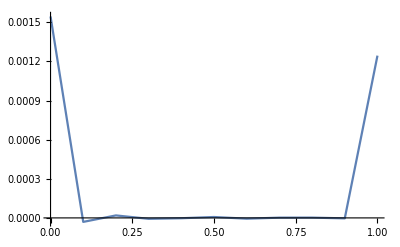

```mathematica
TablePlot[Re[NLS[0][x,0][[1]]],{x,0,1,0.1}]
```

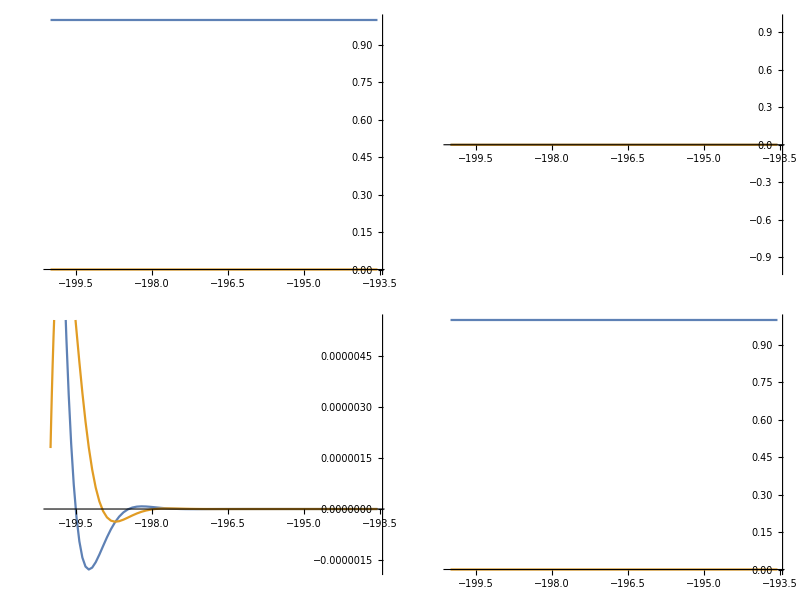
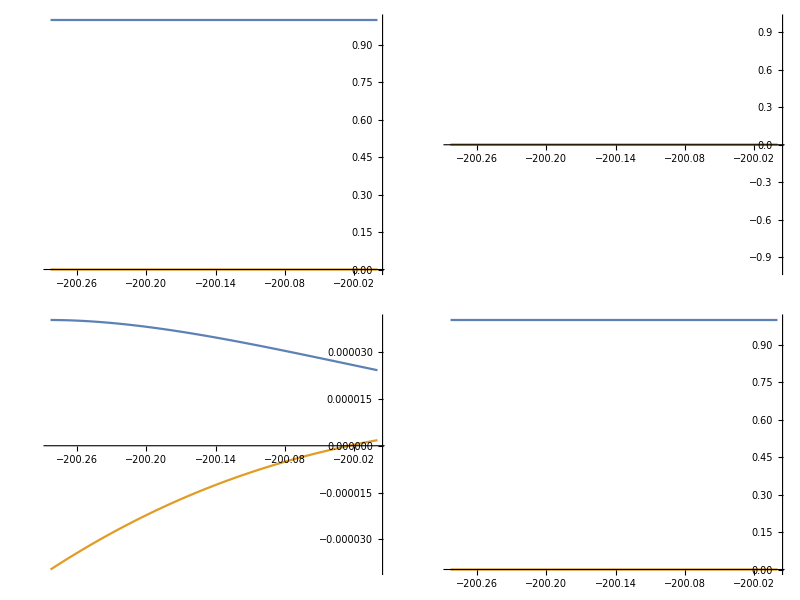
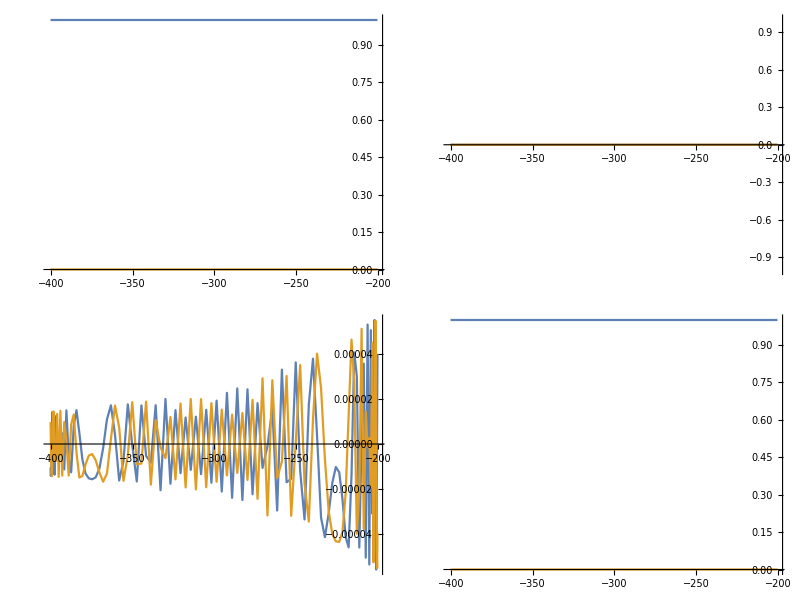
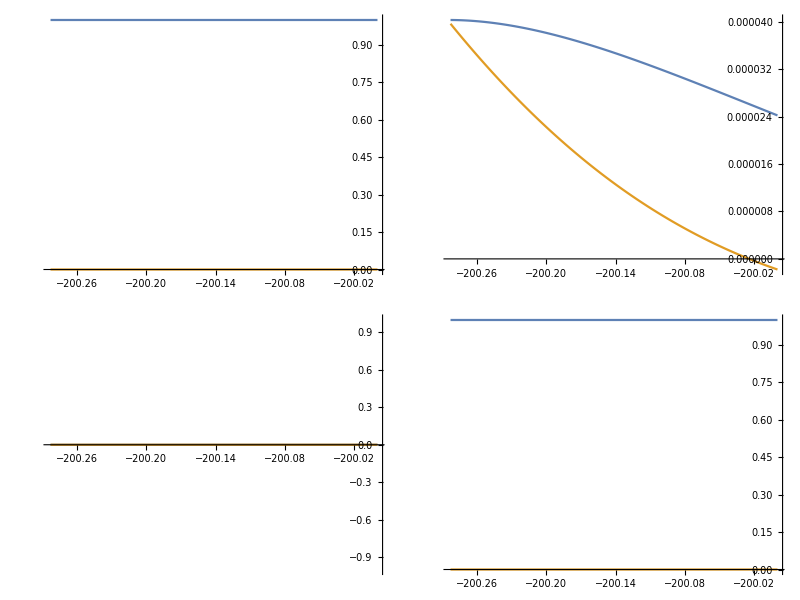
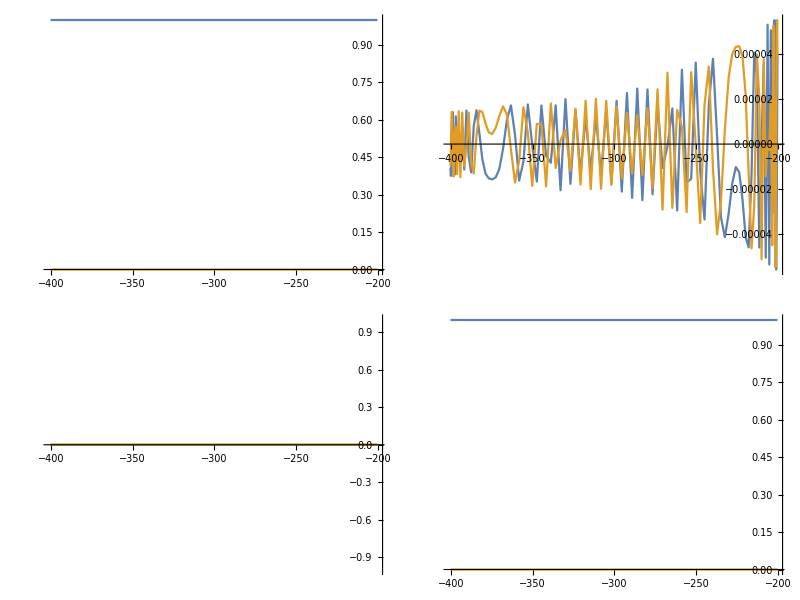
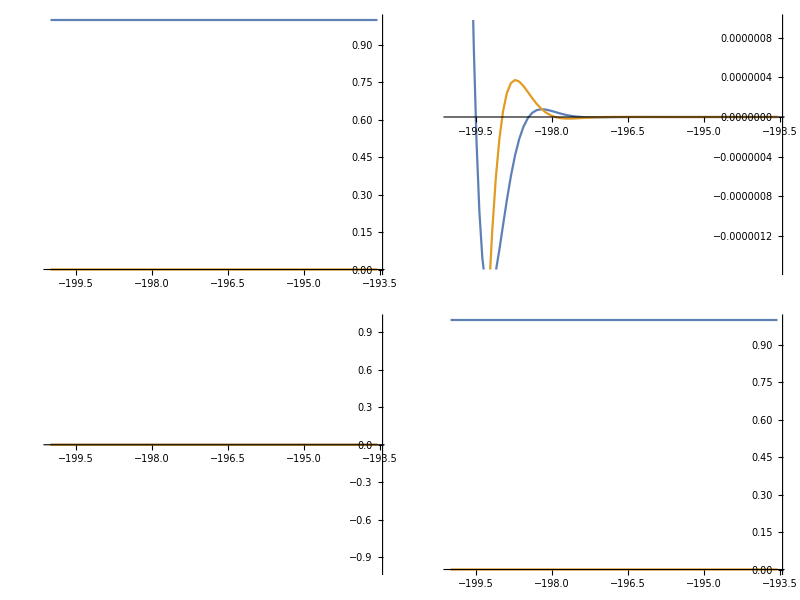
{(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
rhp1
```

```mathematica
mRHWellPosed[rhp1]
```

((1. | 0
0.0000105429-9.75542×10^-6 ⅈ | 1.) | -400.283-0.282843 ⅈ
(1. | 0.0000105429+9.75542×10^-6 ⅈ
0 | 1.) | -400.283+0.282843 ⅈ
(1. | 0
0 | 1.) | -400.
(1. | 0
0 | 1.) | -200.283-0.282843 ⅈ
(1. | 0
0 | 1.) | -200.283+0.282843 ⅈ
(1. | 0
0 | 1.) | -200.
(1. | 0
0 | 1.) | -199.434-0.565685 ⅈ
(1. | 0
0 | 1.) | -199.434+0.565685 ⅈ
(1. | 0
0 | 1.) | -193.544-6.45604 ⅈ
(1. | 0
0 | 1.) | -193.544+6.45604 ⅈ
(1. | 0
0 | 1.) | 0.565685-0.565685 ⅈ
(1. | 0
0 | 1.) | 0.565685+0.565685 ⅈ)

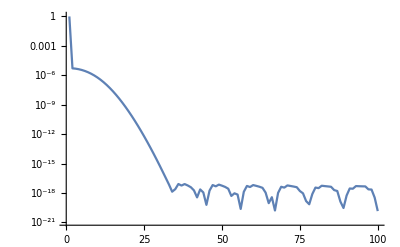
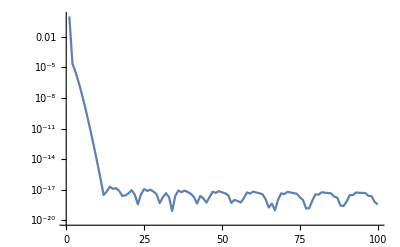
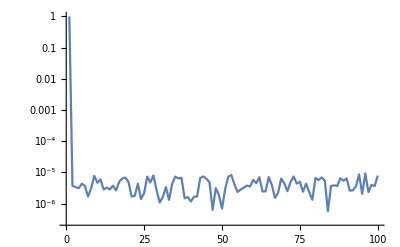
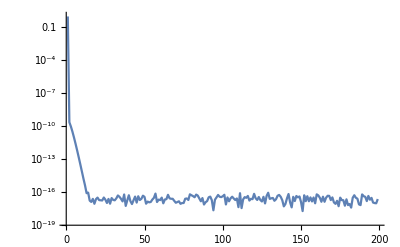
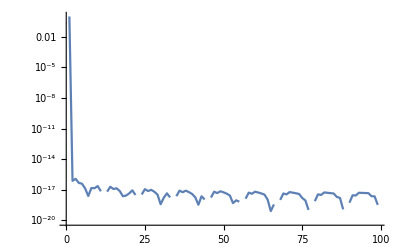
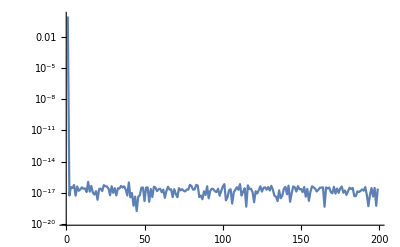
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@rhp1
```

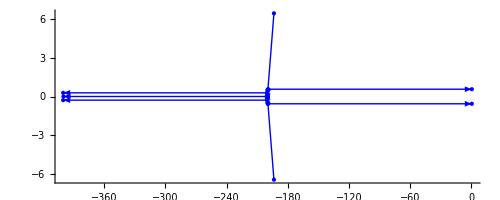

```mathematica
rhp1//DomainPlot
```

```mathematica
Jadapt[0][0,0]
```

{{Private`G1[0,0][#1]&,G2[0,0][#1]&,Private`G3[0,0][#1]&,Private`G4[0,0][#1]&},{Line[{200 ⅈ,0}],Line[{0,-200}],Line[{-200 ⅈ,0}],Line[{0,200}]},{100,100,100,100}}